## Notebook for Homework 1

#### Get the Data

This is the location of the data on an Excel file:

```mathematica
originalFile="/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/Boston2017Hourly.xlsx";
```

```mathematica
(*originalFile2 = "/Users/jaimebuitrago/Dropbox/Jaime/Wolfram Summer School/EnergyJuneMA.xlsx"*)
```

We need to import the data into a variable and then cleanup

```mathematica
sheet=First@Import[originalFile]
```

{{DateHour,Actual},{Sun 1 Jan 2017 00:00:00GMT-4.,1542.56},{Sun 1 Jan 2017 01:00:00GMT-4.,1436.88},8754,{Sun 31 Dec 2017 19:59:59GMT-4.,2293.56},{Sun 31 Dec 2017 20:59:59GMT-4.,2178.72},{Sun 31 Dec 2017 21:59:59GMT-4.,1769.91}}
 |  |  |  |

```mathematica
headers=First@sheet
```

{DateHour,Actual}

```mathematica
data=Map[AssociationThread[headers->#]&,Rest@sheet]
```

{<|DateHour→Sun 1 Jan 2017 00:00:00GMT-4.,Actual→1542.56|>,<|DateHour→Sun 1 Jan 2017 01:00:00GMT-4.,Actual→1436.88|>,8755,<|DateHour→Sun 31 Dec 2017 20:59:59GMT-4.,Actual→2178.72|>,<|DateHour→Sun 31 Dec 2017 21:59:59GMT-4.,Actual→1769.91|>}
 |  |  |  |

```mathematica
data1=Rule@@@data[[All,{"DateHour","Actual"}]]
```

{Sun 1 Jan 2017 00:00:00GMT-4.→1542.56,Sun 1 Jan 2017 01:00:00GMT-4.→1436.88,Sun 1 Jan 2017 02:00:00GMT-4.→1401.3,8753,Sun 31 Dec 2017 19:59:59GMT-4.→2293.56,Sun 31 Dec 2017 20:59:59GMT-4.→2178.72,Sun 31 Dec 2017 21:59:59GMT-4.→1769.91}
 |  |  |  |

I want to use the first 11 months of the year for training, therefore I have to cut the dataset to only the first 11 months = 8016 hours

```mathematica
trainingset=data1[[1;;720]];
```

```mathematica
(*8017*)
```

```mathematica
validationset = data1[[721;;721+24 ]];
(*-31*24+2;;*)
```

```mathematica
dates= trainingset[[All,1]];
values = trainingset[[All,2]];
ts=TimeSeries[values,{dates}]
```

TimeSeries[…]

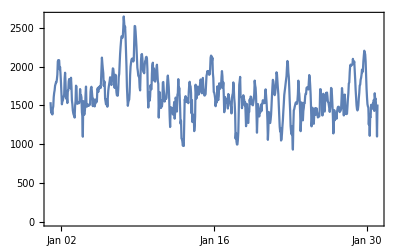

```mathematica
DateListPlot[ts]
```

```mathematica
dates1=validationset[[;;24,1]];
```

```mathematica
(*;;24,1*)
```

```mathematica
values1=validationset[[;;24,2]];
```

```mathematica
ts1=TimeSeries[values1,{dates1}]
```

TimeSeries[…]

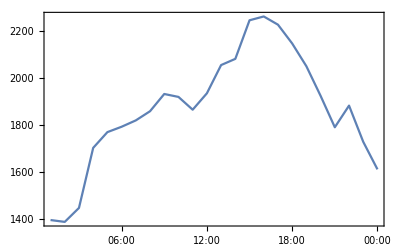

```mathematica
DateListPlot[ts1]
```

```mathematica
forecast=TimeSeriesForecast[ARProcess[{-.2,.4,.6},.1],values,3]
```

1119.55

```mathematica
forecast=TimeSeriesForecast[ARProcess[{-.2,.4,.6},.1],values,{24}]
```

TemporalData[…]

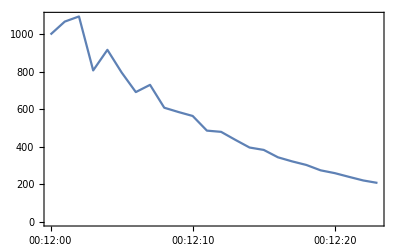

```mathematica
DateListPlot[forecast]
```

```mathematica
tsm=TimeSeriesModelFit[values]
```

TimeSeriesModel[…]

```mathematica
Normal[tsm]
```

ARMAProcess[204.297,{0.875479},{0.233856,0.0819534},10864.4]

```mathematica
tsm[35]
```

1585.41

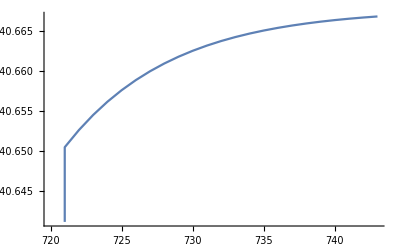

```mathematica
ListLinePlot[TimeSeriesForecast[tsm,{24}]]
```

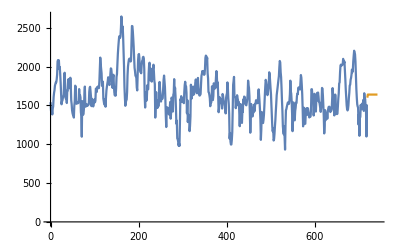

```mathematica
ListLinePlot[{tsm["TemporalData"],TimeSeriesForecast[tsm,{24}]}]
```